get list of splitting events

out degree == 2

```mathematica
FullStabilityGraph50=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/GroupStability/FullStabilityGraph.mx"];
```

```mathematica
splittingEvents50 =Select[VertexList[FullStabilityGraph50],VertexOutDegree[FullStabilityGraph50,#]=== 2&];
```

```mathematica
stablegroup[g_]:=ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]
```

```mathematica
fullgroups50=stablegroup[FullStabilityGraph50];
```

```mathematica
groupsAssoc50=Association[First[#]->#&/@fullgroups50];
```

Weird situation:

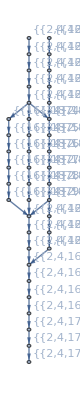

```mathematica
NeighborhoodGraph[FullStabilityGraph50,splittingEvents50[[100]],10,VertexLabels->"Name"]
```

```mathematica
groupPositions[membersTime_]:=Mean[DeleteMissing[rawCoordinates[[membersTime[[1]],Last[membersTime]]]]]
```

```mathematica
groupPositions[{{2,5,11,16,17,45},4217}]
```

{583612.,6.56358×10^6}

```mathematica
Length[splittingEvents50]
```

4849

```mathematica
paths=Function[split,Catch[EuclideanDistance@@@Map[groupPositions,
Transpose[#[[All,;;UpTo[Min[Length/@#]]]]&@Lookup[
groupsAssoc50,
VertexOutComponent[FullStabilityGraph50,split,{1}],
Throw[Nothing]]],
{2}]]]/@splittingEvents50;
```

$Aborted

```mathematica
paths=GeneralUtilities`MonitoredMap[Function[split,Catch[EuclideanDistance@@@Map[groupPositions,
Transpose[#[[All,;;UpTo[Min[Length/@#]]]]&@Lookup[
groupsAssoc50,
VertexOutComponent[FullStabilityGraph50,split,{1}],
Throw[Nothing]]],
{2}]]],splittingEvents50];
```

```mathematica
ListLinePlot[paths[[;;1000]],PlotStyle->Directive[Black,Opacity[1],Thin]]
```

$Aborted[]

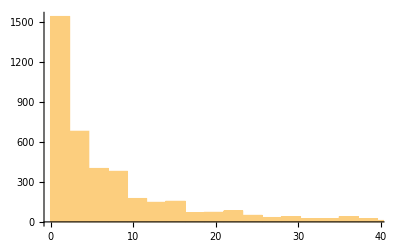

```mathematica
Histogram[Length/@paths]
```

```mathematica
Rasterize[ListLinePlot[Select[paths,Length[#]>5&],PlotStyle->Directive[Black,Opacity[0.5],Thin],Frame->True,FrameLabel->{"Time in steps since splitting","Distance in m"}]]
```

-Graphics-